```mathematica
ClearAll["Global`*"]
SetDirectory["/Users/diegoandrade/Documents/NS/"];
Get[ "/Users/diegoandrade/Desktop/functions.m"]

(* Utilities *)
myPrint[args__,{style__}]:=Print[Row[{args},BaseStyle->{style}]];(* Utility to print info *)
```

```mathematica
(*Inteirior Points*)
imax = 4; (*Number of Cell in X direction *)
jmax = 4; (*Number of Cell in Y direction *)
xlength =1;
ylenght =1;
delx = 1/(imax);(* Spatial step interval in X direction *)
dely = 1/(jmax); (* Spatial step interval in Y direction *)
ustar=1; (* normalized velocity of lid *)
```

```mathematica
(* Time conditions *)
(* Initialize time value and time index *) 
timet=0;timen=0;(* timet:time value,timen:time index *)
delt = 0.02;  (*Time Step*)
tau = 0.5; (*Safety factor for time step size control τ*)
tend=6;
```

```mathematica
(*Pressure Itertion Data *)
it = 0;(* SOR counter  *)
res = 0;  (* Norm of pressure equation residual*)
eps = 0.001; (* Stopping tolerance for pressure iteration*)
gamma = 0.9;(*Upwind differencing factor γ*)
```

```mathematica
(*Problem Dependent quatities *)
(*Rey= 1000; (*Reynolds Number*)*)
Reynolds = List[1,10,100,1000,5000,10000];
GX = 0;(* Body forces *)
GY= 0;(* Body forces *)
UI = 0;  (* Initial Velocity *)
VI =0; (* Initial Velocity *)
PI = 0; (* Initial Pressure *)
Umed = 1; (*Mean velocity Value of the lid *)
itermax=100;(* Max iteration in SOR *)
omega=1.7;(* SOR Relaxatioxn*)
TOL=0.001;(* SOR Tolerance*)
rindex=4;
```

```mathematica
(*Data Array Initialization *)
(*initialize and assign initial values to u,v,and p*)
U = Table[0,{imax+2},{jmax+2}];(* Velocity in x-direction *)
V = Table[0,{imax+2},{jmax+2}];(* Velocity in y-direction *)
P= Table[0,{imax+2},{jmax+2}] ;(* Pressure *)
wW=2;wE=2;wN=2;wS=2; (*flags to indicate no slip condition on a wall *)

(*Saving info*)
SU= Table[U,1*Round[tend]];
SV=Table[V,1*Round[tend]];

(*Saving Reynolds info info*)
RU= Table[U,Length[Reynolds]];
RV=Table[V,Length[Reynolds]];

(*F= Table[0,{imax+2},{jmax+2}]; (* F *)
G= Table[0,{imax+2},{jmax+2}]; (* G *)*)
GSV=Table[0,{(imax)*(jmax)}];(*Vector initialization for gauss seidel*)
```

```mathematica
(*Boundary Correction*)
(*U[[All,jmax+2 ]]=2*Umed-U[[All,jmax+1]] ;(*CORRECT THIS *)
U[[1,jmax+2]]=0.0; (*@ the wall *)
U[[imax+2,jmax+2]]=0.0; (* @ the wall *)*)
U=boundaryValuesU[U,ustar,imax,jmax,wN,wE,wW,wS];
V=boundaryValuesV[V,imax,jmax,wN,wE,wW,wS];
```

```mathematica
(* compute F and G according to Eqs.(3.36) and (3.37) *)
(* compute (d^2 u/d x^2) *)
d2ux = deriv2ux[U,imax,jmax,delx];
(* compute (d^2 u/d y^2) *)
d2uy = deriv2uy[U,imax,jmax,dely];
(* compute (d u^2/d x) *)
d1u2x=deriv1u2x[U,imax,jmax,delx, gamma];
(* compute (d uv/d y) *)
d1uvy=deriv1uvy[U,V,imax,jmax,dely,gamma];
(* compute (d^2 v/d x^2) *)
d2vx=deriv2vx[V,imax,jmax,delx];
(* compute (d^2 v/d y^2) *)
d2vy=deriv2vy[V,imax,jmax,dely];
(* compute (d v^2/d y) *)
d1v2y=deriv1v2y[V,imax,jmax,dely,gamma];
(* compute (d uv/d x) *)
d1uvx=deriv1uvx[U,V,imax,jmax,delx,gamma];
```

```mathematica
(* compute F and G *)
F=compF[U,imax,jmax,delx,delt,Reynolds[[rindex]],GX,d2ux,d2uy,d1u2x,d1uvy];
G= compG[V,imax,jmax,dely,delt,Reynolds[[rindex]],GY,d2vx,d2vy,d1uvx,d1v2y];
```

```mathematica
(* compute right-hand size of the pressure Eq.(3.38) *)
RHS=computeRHS[imax,jmax,delt,delx,dely,F,G];
```

```mathematica
(*Perform SOR*)
iter=0; (* index for iterative SOR *)
ritnorm=1;  (* tolerance (at first,it is set a large number) *)

While[ (iter<itermax && ritnorm>eps),
(* compute p of the next step, pNew *)
pNew = computepNew[imax,jmax,omega,delx,dely,P,RHS];
(* compute residual for pressure Eq.according to Eq.(3.45) *)
rit = computeRit[imax,jmax,delx,dely,P,RHS];
(* compute L^2 norm of residual according to Eq.(3.46) *)
   ritnorm=Norm[rit,Frobenius]/(imax+2)*(jmax+2);
(* update p *)
P=pNew;
(* increment counter *)
iter=iter+1;
]
```

```mathematica
(* compute u and v of the next step according to Eqs.(3.34) and (3.35) *)
```

```mathematica
U=computeU[U,imax,jmax,delt,delx,F,P];
V=computeV[V,imax,jmax,delt,dely,G,P].00;
timet=timet+delt;
timen=timen+1;
```

```mathematica
k=1; (*to save info after each time iteration*)
```

```mathematica
(* iterations after 1st iteration are written below *)
```

```mathematica
While[ timet < tend,
(*  select delta t according Eq.(3.50) after 1st time step *)
	delt=selectDelta[tau,Reynolds[[rindex]],delx,dely,U,V];
(* set boundary values for velocity u and v*)
	U=boundaryValuesU[U,ustar,imax,jmax,wN,wE,wW,wS];
	V=boundaryValuesV[V,imax,jmax,wN,wE,wW,wS];

(* compute F and G according to Eqs.(3.36) and (3.37) *)
(* compute (d^2 u/d x^2) *)
	d2ux = deriv2ux[U,imax,jmax,delx];
(* compute (d^2 u/d y^2) *)
	d2uy = deriv2uy[U,imax,jmax,dely];
(* compute (d u^2/d x) *)
	d1u2x=deriv1u2x[U,imax,jmax,delx, gamma];
(* compute (d uv/d y) *)
	d1uvy=deriv1uvy[U,V,imax,jmax,dely,gamma];
(* compute (d^2 v/d x^2) *)
	d2vx=deriv2vx[V,imax,jmax,delx];
(* compute (d^2 v/d y^2) *)
	d2vy=deriv2vy[V,imax,jmax,dely];
(* compute (d v^2/d y) *)
	d1v2y=deriv1v2y[V,imax,jmax,dely,gamma];
(* compute (d uv/d x) *)
	d1uvx=deriv1uvx[U,V,imax,jmax,delx,gamma];

(* set boundary values for pressure p,and F and G *)
P = boundaryValuesP[P,imax,jmax,wN,wE,wW,wS];
F=boundaryValuesF[U,imax,jmax,wN,wE,wW,wS];
G = boundaryValuesG[V,imax,jmax,wN,wE,wW,wS];

(* compute F and G *)
F=compF[U,imax,jmax,delx,delt,Reynolds[[rindex]],GX,d2ux,d2uy,d1u2x,d1uvy];
G= compG[V,imax,jmax,dely,delt,Reynolds[[rindex]],GY,d2vx,d2vy,d1uvx,d1v2y];

(* compute right-hand size of the pressure Eq.(3.38) *)
RHS=computeRHS[imax,jmax,delt,delx,dely,F,G];

(*Perform SOR*)
iter=0; (* index for iterative SOR *)
ritnorm=1;  (* tolerance (at first,it is set a large number) *)

While[ (iter<itermax && ritnorm>eps),
	(* compute p of the next step, pNew *)
	pNew = computepNew[imax,jmax,omega,delx,dely,P,RHS];
	(* compute residual for pressure Eq.according to Eq.(3.45) *)
	rit = computeRit[imax,jmax,delx,dely,P,RHS];
	(* compute L^2 norm of residual according to Eq.(3.46) *)
	        ritnorm=Norm[rit,Frobenius]/(imax+2)*(jmax+2);
	(* update p *)
	P=pNew;
	(* increment counter *)
	iter=iter+1;
	];

	U=computeU[U,imax,jmax,delt,delx,F,P];
	V=computeV[V,imax,jmax,delt,dely,G,P].00;
(* Prints Values after 10 iterations *)
	If[QuotientRemainder[timen,200][[2]]==0,Print["it# = " ,timen, " timet = ",timet ]];

(* For a videoclip saving info every second*)
If[(timet<k/1 && k/1≤timet+delt),
SU[[k]]=U;SV[[k]]=V;
(*Print[Style["Simulating at ",N[k/4], " seconds currently ..."];*)
myPrint["Simulating at ",N[k/1], " seconds currently ...",{FontSize->10,FontWeight->Bold,Background->LightGreen}];
k++;
];

(*	If[(timet<1.4&&1.4≤timet+delt),
		SU[[1]]=U;
		SV[[1]]=V;
,If[(timet<2.4&&2.4≤timet+delt),
		SU[[2]]=U;
		SV[[2]]=V;
,If[(timet<3.4&&3.4≤timet+delt),
		SU[[3]]=U;
		SV[[3]]=V;
,If[(timet<4.4&&4.4≤timet+delt),
		SU[[4]]=U;
		SV[[4]]=V;
,If[(timet<5.4&&5.4≤timet+delt),
		SU[[5]]=U;
		SV[[5]]=V;
,If[(timet<6.4&&6.4≤timet+delt),
		SU[[6]]=U;
		SV[[6]]=V;
,If[(timet<15.0&&15.0≤timet+delt),
		SU[[6]]=U;
		SV[[6]]=V;
,If[(timet<35.0&&35.0≤timet+delt),
		SU[[6]]=U;
		SV[[6]]=V;
]]]]]]]]; *)

(*increment counter*)
timet=timet+delt;
timen++;
];
```

Simulating at 1. seconds currently ...

Simulating at 2. seconds currently ...

it# = 200 timet = 2.94647

Simulating at 3. seconds currently ...

Simulating at 4. seconds currently ...

Simulating at 5. seconds currently ...

it# = 400 timet = 5.88765

Simulating at 6. seconds currently ...

Simulating at 7. seconds currently ...

Simulating at 8. seconds currently ...

it# = 600 timet = 8.82882

Simulating at 9. seconds currently ...

Simulating at 10. seconds currently ...

```mathematica
MatrixForm[U]
MatrixForm[V]
```

(0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0
0.000590912 | -0.000510237 | -0.000750589 | -0.000824357 | -0.000892472 | -0.000963903 | -0.00104503 | -0.00113039 | -0.00123278 | -0.00134814 | -0.00149846 | -0.00171739 | -0.00206589 | -0.00268641 | -0.00388813 | -0.00639322 | -0.0115021 | 0.0385484 | 1.96145
0.00131647 | -0.00123463 | -0.00176463 | -0.00192276 | -0.00205317 | -0.00219483 | -0.00235947 | -0.0025501 | -0.00276619 | -0.00301709 | -0.00331546 | -0.00370999 | -0.00429472 | -0.00523387 | -0.0068232 | -0.0094625 | -0.0113332 | 0.0640663 | 1.93593
0.00201643 | -0.00197741 | -0.00277144 | -0.00299859 | -0.00317877 | -0.00339636 | -0.00365712 | -0.00396031 | -0.0042967 | -0.00466278 | -0.00507099 | -0.00555648 | -0.00620062 | -0.00714898 | -0.00860195 | -0.0106054 | -0.0091755 | 0.0832479 | 1.91675
0.00268495 | -0.00268306 | -0.00371653 | -0.00399559 | -0.00423962 | -0.00454304 | -0.00491805 | -0.00534562 | -0.00580766 | -0.00628034 | -0.00675337 | -0.00724344 | -0.00780526 | -0.00854583 | -0.00960728 | -0.0108338 | -0.00666735 | 0.0989653 | 1.90103
0.00331855 | -0.00331509 | -0.00455246 | -0.00489665 | -0.00521724 | -0.0056332 | -0.00614133 | -0.00671332 | -0.00731184 | -0.00789413 | -0.00841633 | -0.00885315 | -0.00922171 | -0.00959694 | -0.0101173 | -0.0105456 | -0.00408618 | 0.112524 | 1.88748
0.00386403 | -0.00386377 | -0.00527387 | -0.00568665 | -0.00610335 | -0.00664669 | -0.00730667 | -0.00805429 | -0.00882747 | -0.00955725 | -0.0101552 | -0.010532 | -0.010626 | -0.0104819 | -0.0102702 | -0.00981807 | -0.00138317 | 0.124614 | 1.87539
0.00430822 | -0.00429682 | -0.00585495 | -0.00633959 | -0.00685914 | -0.00754186 | -0.00838707 | -0.00935119 | -0.0103772 | -0.0113505 | -0.0121207 | -0.0124896 | -0.012273 | -0.0113934 | -0.0101224 | -0.00854928 | 0.00168369 | 0.135654 | 1.86435
0.00461242 | -0.00460719 | -0.00626125 | -0.00680898 | -0.00743093 | -0.00827 | -0.00933133 | -0.0105894 | -0.0119749 | -0.0133537 | -0.0144908 | -0.0150407 | -0.0145617 | -0.0126358 | -0.00964247 | -0.00642408 | 0.00546201 | 0.145979 | 1.85403
0.00475772 | -0.00476612 | -0.00645361 | -0.00704686 | -0.00776712 | -0.00876971 | -0.0100797 | -0.0116968 | -0.01359 | -0.0156043 | -0.0174582 | -0.0186128 | -0.0181768 | -0.0147378 | -0.00878978 | -0.00293945 | 0.0105928 | 0.155891 | 1.84412
0.00472087 | -0.00473709 | -0.00638634 | -0.00701002 | -0.00781276 | -0.00896331 | -0.01052 | -0.0125415 | -0.0150859 | -0.0180235 | -0.0211437 | -0.0237303 | -0.0241859 | -0.0186592 | -0.00758598 | 0.00253141 | 0.0180668 | 0.16577 | 1.83424
0.00447878 | -0.00449291 | -0.00603604 | -0.00666318 | -0.00750785 | -0.00874354 | -0.0104949 | -0.0129021 | -0.0161499 | -0.0203272 | -0.0254412 | -0.0307765 | -0.0336959 | -0.0258482 | -0.00638715 | 0.0103477 | 0.0289602 | 0.176147 | 1.82387
0.00402272 | -0.00402791 | -0.00540082 | -0.00598935 | -0.00679735 | -0.00801641 | -0.00980378 | -0.0124333 | -0.0162967 | -0.0219228 | -0.0297587 | -0.0394157 | -0.0466943 | -0.0376941 | -0.00666022 | 0.0199286 | 0.0434019 | 0.187583 | 1.81244
0.00336017 | -0.00335748 | -0.00450085 | -0.00499282 | -0.00567374 | -0.00671037 | -0.00828948 | -0.0107681 | -0.0148636 | -0.0217754 | -0.0328567 | -0.0478453 | -0.0606559 | -0.0537648 | -0.0121467 | 0.0296808 | 0.0589109 | 0.19962 | 1.80041
0.00252154 | -0.00251706 | -0.00337889 | -0.003726 | -0.00418908 | -0.00487608 | -0.00592092 | -0.00768453 | -0.0111833 | -0.0185754 | -0.0325192 | -0.0527115 | -0.0704627 | -0.0696112 | -0.0311587 | 0.0404867 | 0.0692385 | 0.208795 | 1.79122
0.00156605 | -0.00156371 | -0.00211244 | -0.00229491 | -0.0024992 | -0.00274593 | -0.00301572 | -0.00345442 | -0.00510975 | -0.0110616 | -0.0257093 | -0.0490581 | -0.0711233 | -0.0768232 | -0.0492446 | 0.026071 | 0.0756965 | 0.204049 | 1.79597
0.000604202 | -0.000602997 | -0.000843197 | -0.000886125 | -0.000892013 | -0.000813485 | -0.000478609 | 0.000397515 | 0.00158516 | -0.000112272 | -0.0112023 | -0.0312855 | -0.0523542 | -0.0658948 | -0.059976 | -0.0197198 | 0.066949 | 0.176127 | 1.8239
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0)

(0 | -0.000508097 | -0.00128679 | -0.00215013 | -0.00307244 | -0.00404036 | -0.00507836 | -0.00619543 | -0.00742236 | -0.00876708 | -0.0102645 | -0.0119841 | -0.0140536 | -0.0167445 | -0.0206375 | -0.0270357 | -0.0385424 | 0 | 0
0. | 0.000570145 | 0.00137642 | 0.00222007 | 0.0030932 | 0.00404655 | 0.00507421 | 0.00620025 | 0.00742134 | 0.00876491 | 0.0102652 | 0.0119809 | 0.014049 | 0.0167445 | 0.0206425 | 0.0270439 | 0.0385513 | 0 | 0.
0. | 0.00076005 | 0.00176403 | 0.00282543 | 0.00394687 | 0.00516104 | 0.00647407 | 0.00789364 | 0.00943645 | 0.0111056 | 0.0129251 | 0.0149251 | 0.0171543 | 0.0196994 | 0.0226333 | 0.0256994 | 0.025525 | 0 | 0.
0. | 0.000741655 | 0.00172132 | 0.00276965 | 0.00389475 | 0.00510926 | 0.00642166 | 0.0078424 | 0.00937831 | 0.0110293 | 0.0127823 | 0.0146213 | 0.0165219 | 0.0184297 | 0.0202023 | 0.0213429 | 0.0191836 | 0 | 0.
0. | 0.000686987 | 0.00160411 | 0.00260825 | 0.00368519 | 0.00485626 | 0.00612743 | 0.00751651 | 0.00902446 | 0.0106349 | 0.0123123 | 0.0139939 | 0.0155908 | 0.0169843 | 0.0179926 | 0.0182244 | 0.0157167 | 0 | 0.
0. | 0.000615531 | 0.00145984 | 0.00238181 | 0.00338421 | 0.00448173 | 0.00570006 | 0.00705487 | 0.00855238 | 0.0101627 | 0.011823 | 0.0134329 | 0.0148503 | 0.0159063 | 0.0164201 | 0.0161357 | 0.0135585 | 0 | 0.
0. | 0.000533818 | 0.00127074 | 0.00207992 | 0.00297024 | 0.0039736 | 0.00512801 | 0.0064565 | 0.0079703 | 0.00964068 | 0.0113863 | 0.0130643 | 0.0144736 | 0.0153598 | 0.0155189 | 0.0147943 | 0.0120901 | 0 | 0.
0. | 0.000436186 | 0.00102537 | 0.00168174 | 0.00242872 | 0.00331368 | 0.0043805 | 0.00568347 | 0.00724074 | 0.00904264 | 0.0110095 | 0.01297 | 0.0146136 | 0.0155302 | 0.0153778 | 0.0141076 | 0.0110422 | 0 | 0.
0. | 0.000304319 | 0.000711938 | 0.00117935 | 0.00174754 | 0.0024687 | 0.00341634 | 0.00465766 | 0.0062675 | 0.00827247 | 0.0106412 | 0.0131861 | 0.0154725 | 0.0167091 | 0.0162333 | 0.0141054 | 0.0103245 | 0 | 0.
0. | 0.000141624 | 0.000331219 | 0.000572266 | 0.000909749 | 0.0014074 | 0.00215775 | 0.00327272 | 0.0048892 | 0.00713632 | 0.0100964 | 0.0136631 | 0.0172787 | 0.019381 | 0.0185232 | 0.0150423 | 0.00991264 | 0 | 0.
0. | -0.0000442836 | -0.000105663 | -0.000135571 | -0.0000920159 | 0.0000967018 | 0.00053785 | 0.00138479 | 0.00287515 | 0.00529185 | 0.00897317 | 0.0140909 | 0.0200984 | 0.0240252 | 0.0228239 | 0.0173501 | 0.00987768 | 0 | 0.
0. | -0.000248437 | -0.000585552 | -0.000927824 | -0.0012421 | -0.00146323 | -0.00149365 | -0.00113315 | -0.0000671631 | 0.00223173 | 0.00653134 | 0.0135819 | 0.0230968 | 0.030283 | 0.0290863 | 0.021271 | 0.0103764 | 0 | 0.
0. | -0.00046041 | -0.00108415 | -0.00176337 | -0.00247705 | -0.00321374 | -0.00389806 | -0.00436858 | -0.00421877 | -0.00261918 | 0.00169958 | 0.0103406 | 0.0233419 | 0.0351879 | 0.0354564 | 0.0258762 | 0.011436 | 0 | 0.
0. | -0.000663246 | -0.00156222 | -0.002563 | -0.00369373 | -0.00499598 | -0.00651063 | -0.00816611 | -0.00960086 | -0.00974738 | -0.00664712 | 0.00178262 | 0.0157404 | 0.0318114 | 0.0372977 | 0.0275444 | 0.0120361 | 0 | 0.
0. | -0.000836594 | -0.00196177 | -0.00323221 | -0.00471854 | -0.00654884 | -0.00891217 | -0.0119961 | -0.0156752 | -0.0188786 | -0.0192175 | -0.0143511 | -0.0045446 | 0.0112985 | 0.0303103 | 0.0195039 | 0.0091762 | 0 | 0.
0. | -0.000953479 | -0.00222149 | -0.00365509 | -0.00534231 | -0.00747081 | -0.0103737 | -0.0146073 | -0.0206844 | -0.0281985 | -0.0350086 | -0.038663 | -0.0380022 | -0.0307918 | -0.0127063 | 0.00171155 | -0.00474563 | 0 | 0.
0. | -0.000960991 | -0.00223084 | -0.00363985 | -0.00524583 | -0.0071781 | -0.0097178 | -0.0135719 | -0.0202684 | -0.0312172 | -0.0457229 | -0.0634939 | -0.0822628 | -0.0931903 | -0.0824596 | -0.0366691 | -0.0279222 | 0 | 0.
0. | -0.000603098 | -0.00144706 | -0.00233301 | -0.00322511 | -0.00403891 | -0.00451856 | -0.00412066 | -0.00253368 | -0.00264427 | -0.0138447 | -0.0451293 | -0.0974856 | -0.16338 | -0.223356 | -0.243076 | -0.176127 | 0 | 0.
0 | 0.000604107 | 0.00144738 | 0.0023341 | 0.00322822 | 0.00404529 | 0.00452985 | 0.00414463 | 0.00257617 | 0.00268062 | 0.0138163 | 0.0450126 | 0.0972987 | 0.163167 | 0.223177 | 0.242989 | 0.176097 | 0 | 0)

```mathematica
(*This function is used to plot the vector field creates a field that VectorFormUV can read ListVectorPlot*)
VectorFormUV[MatU_,MatV_,imax_,jmax_]:=
Module[{U=MatU,V=MatV,m=imax,n=jmax,S},
S=Table[{U[[i,j]],V[[i,j]]},{i,1,n+2},{j,1,m+2}];
Return[S];
];
```

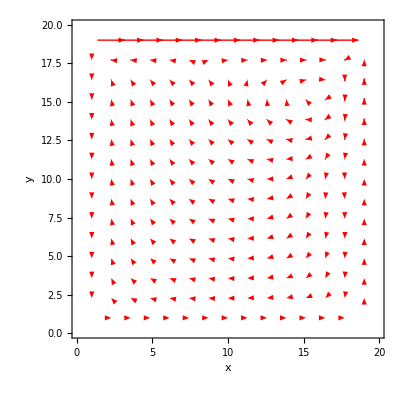

```mathematica
ListVectorPlot[VectorFormUV[U,V,imax,jmax],FrameLabel->{x,y},PerformanceGoal->"Speed",VectorStyle->Red]
```

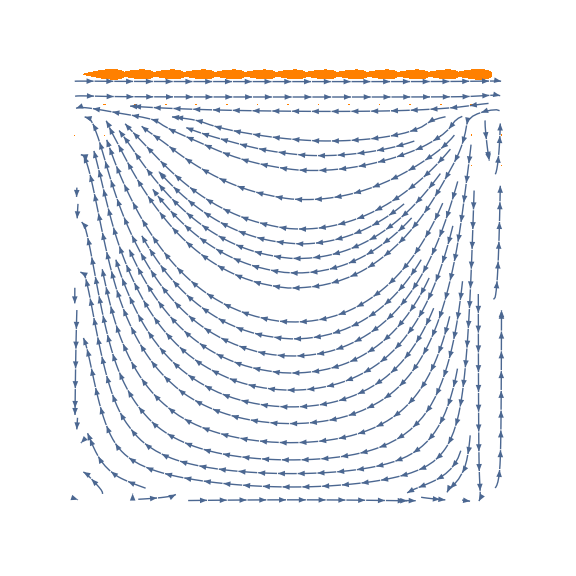

```mathematica
ListVectorPlot[VectorFormUV[SU[[2]],SV[[2]],imax,jmax],FrameLabel->{x,y},Frame->None,PerformanceGoal->"Quality",VectorStyle->{{Orange,"Drop"},{Green,"Dart"}},StreamPoints->45,StreamScale->Tiny,StreamScale->Tiny,AspectRatio->Automatic,PlotLegends->Automatic,ImageSize->Large]
```